# 矩阵分解

## Cholesky分解

## 二次曲面

```mathematica
plotQuadratic[a_,b_,c_]:=#[a x1^2+2 b x1 x2+c x2^2,{x1,-2,2},{x2,-2,2},PlotTheme->"Minimal"]&/@{Plot3D,ContourPlot}
```

```mathematica
Manipulate[plotQuadratic[a,b,c],{a,-2,2},{b,-2,2},{c,-2,2}]
```

## 格拉姆矩阵的Cholesky分解

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"];
{sepalLength,sepalWidth,petalLength,petalWidth}=Table[irisData[[i,1,j]],{j,1,4},{i,1,150}];
irisGram=#.Transpose[#]&@{sepalLength,sepalWidth,petalLength,petalWidth};
```

```mathematica
String2Pic[string_]:=Rasterize[Text[string],RasterSize->100,ImageSize->50](*将符号转化为图片*)
CholeskyMatrixPlot[matrix_]:=Module[{plots},
plots=MatrixPlot[#,PlotTheme->"Minimal",AspectRatio->1,ImageSize->Small]&/@{matrix,Transpose@#,#}&@CholeskyDecomposition[matrix];
GraphicsRow[{plots[[1]],String2Pic["="],plots[[2]],String2Pic["@"],plots[[3]]},ImageSize->500]
]
```

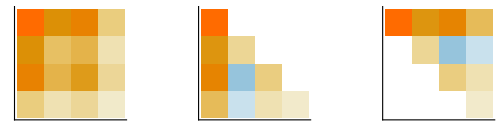

```mathematica
CholeskyMatrixPlot[irisGram]
```

## 余弦相似度矩阵

```mathematica
irisScalingMatrix=DiagonalMatrix[Norm/@{sepalLength,sepalWidth,petalLength,petalWidth}]
```

{{72.2762,0.,0.,0.},{0.,37.8206,0.,0.},{0.,0.,50.8204,0.},{0.,0.,0.,17.3876}}

```mathematica
irisCosineSimilarityMatrix=Inverse[irisScalingMatrix].irisGram.Inverse[irisScalingMatrix]
```

{{1.,0.978013,0.948451,0.897691},{0.978013,1.,0.871097,0.808821},{0.948451,0.871097,1.,0.98355},{0.897691,0.808821,0.98355,1.}}

```mathematica
irisAnglesMatrix=ArcCos@irisCosineSimilarityMatrix/Degree (*单位为度*)
```

{{1.47878×10^-6,12.037,18.4769,26.1438},{12.037,2.25887×10^-6,29.4136,36.0191},{18.4769,29.4136,0.+1.20742×10^-6 ⅈ,10.4069},{26.1438,36.0191,10.4069,0.}}

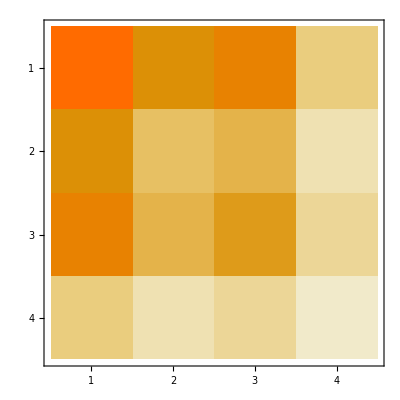
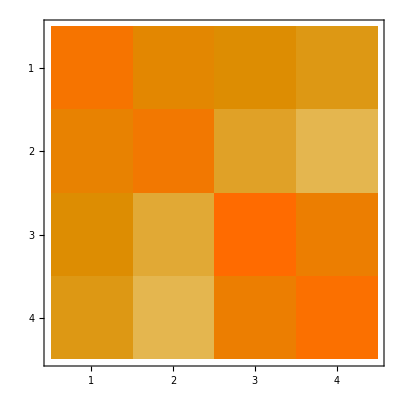
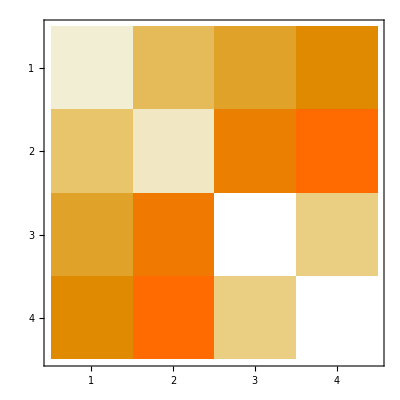

```mathematica
MatrixPlot/@{irisGram,irisCosineSimilarityMatrix,irisAnglesMatrix}(*格拉姆矩阵、余弦相似度矩阵、角度矩阵*)
```

## 特征值分解

谱分解
——对称矩阵的特征值分解

```mathematica
SpectralMatrixPlot[matrix_]:=Module[{eig,plots},
eig=Eigensystem@matrix;
plots={MatrixPlot[matrix,PlotTheme->"Minimal"],MatrixPlot[Rescale[eig[[1,#]]TensorProduct[eig[[2,#]],eig[[2,#]]](*谱分解为四项，决定特征向量重要性的是特征值大小*),MinMax@Flatten@irisGram](*将矩阵归一化，方便热图显示矩阵值的大小*),PlotTheme->"Minimal"]&/@{1,2,3,4}};
GraphicsRow[{plots[[1]],String2Pic["≈"],plots[[2,1]],String2Pic["+"],plots[[2,2]],String2Pic["+"],plots[[2,3]],String2Pic["+"],plots[[2,4]]},ImageSize->600]
]
```

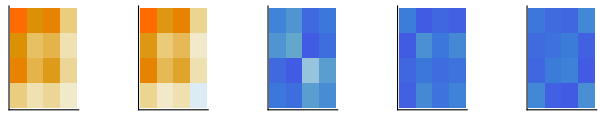

```mathematica
SpectralMatrixPlot[irisGram](*对格拉姆矩阵谱分解*)
```

复数特征值

-Graphics-

```mathematica
rotationTransformationPlot[θ_,r_]:=Module[{a,initialPoints,trajectories},
initialPoints=Table[{a Cos[theta],a Sin[theta]},{theta,Range[0,2 Pi,2 Pi/18]}]/.If[r>1,a->0.13,a->5];(*根据r值确定初始点*)
trajectories=Table[NestList[r RotationMatrix[θ].#&,initialPoints[[i]],20],{i,Length[initialPoints]}];(*迭代20步*)
Show[Graphics[{PointSize[Medium],Point[initialPoints]},PlotRange->{{-5,5},{-5,5}}](*初始点*),ListLinePlot[trajectories,PlotMarkers->{▲,5},PlotTheme->"Minimal",AspectRatio->1,PlotRange->All,PlotStyle->ResourceFunction["SampleColors"]["Rainbow",18]]]]
```

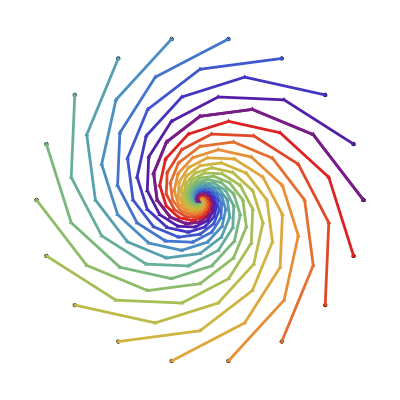
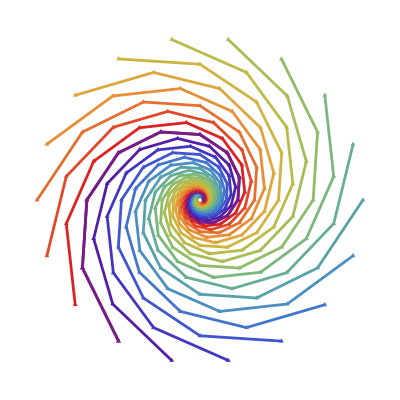

```mathematica
rotationTransformationPlot[30 Degree,#]&/@{0.8,1.2}
```

矩阵开方

```mathematica
MatrixFunction[Sqrt,Rationalize@{{1.25,-0.75},{-0.75,1.25}}]
```

{{3/(2 √2),-1/(2 √2)},{-1/(2 √2),3/(2 √2)}}

斐波那契数列通项

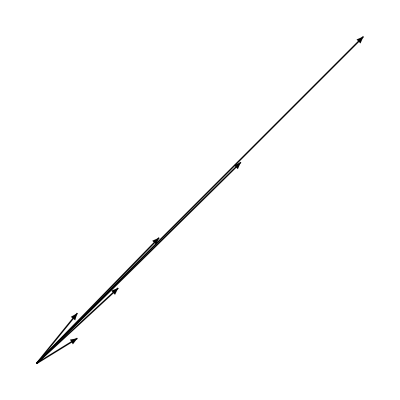

```mathematica
Graphics[Arrow[{{0,0},#}]&/@Partition[Fibonacci[Range[7]](*生成斐波那契数列*),2,1](*将斐波那契数列连续每两项写成列向量形式*),GridLines->Automatic,AspectRatio->1]
```

```mathematica
Simplify[FunctionExpand[Fibonacci[n]],Assumptions->Element[n,Integers]]
```

(-(-2/(1+√5))^n+(1/2 (1+√5))^n)/(√5)

马尔可夫过程的平稳分布

```mathematica
markovProcess[t_,pi_,n_]:=ListLinePlot[Transpose@NestList[t.#&,pi,n],PlotTheme->"Detailed",PlotLegends->{"🐇","🐓"},PlotRange->{0,1},PlotMarkers->{Automatic,5}]
(*T为转移矩阵，Pi包含鸡兔初始数量*)
```

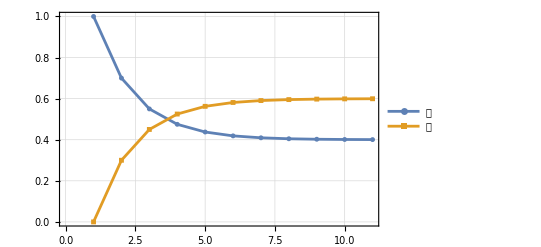
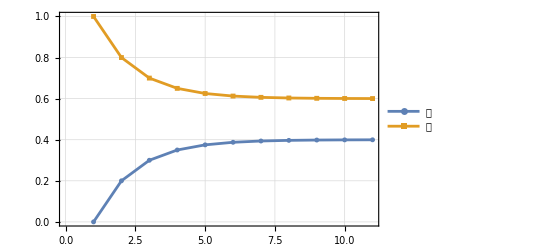
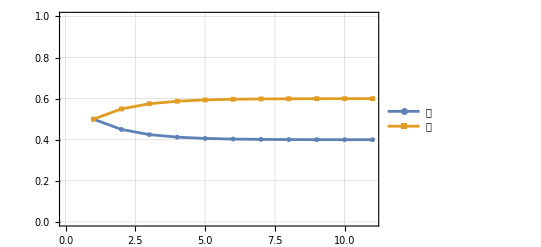
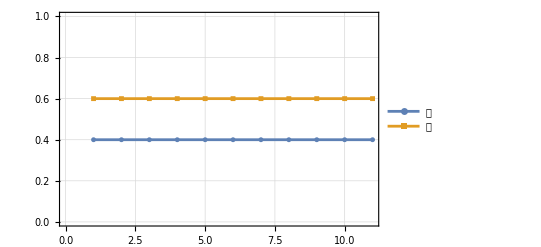

```mathematica
markovProcess[{{0.7,0.2},{0.3,0.8}},#,10]&/@{{1,0},{0,1},{0.5,0.5},{0.4,0.6}}
```

瑞利商

```mathematica
contourRayleighQuotient[A_]:=ContourPlot[Evaluate[{{x1,x2}}.A.Transpose[{{x1,x2}}]],{x1,x2}∈Disk[],Contours->20,ContourStyle->None,ColorFunction->"ThermometerColors",PlotTheme->"Detailed"] (*绘制瑞利商的分子*)
```

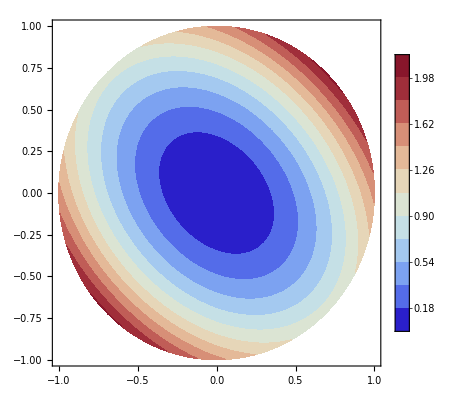
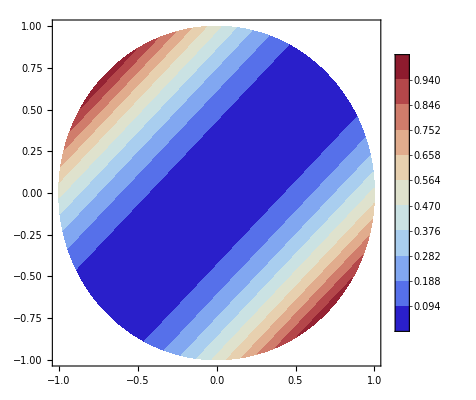
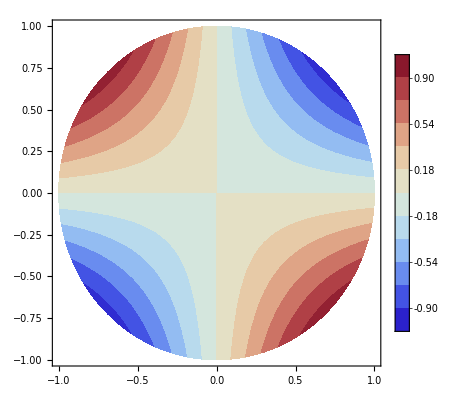

```mathematica
contourRayleighQuotient[#]&/@{{{1.5,0.5},{0.5,1.5}},{{0.5,-0.5},{-0.5,0.5}},{{0,-1},{-1,0}}}
```

```mathematica
Eigenvalues[#]&/@{{{1.5,0.5},{0.5,1.5}},{{0.5,-0.5},{-0.5,0.5}},{{0,-1},{-1,0}}} (*使用特征值计算瑞利商的最值*)
```

{{2.,1.},{1.,0.},{-1,1}}

```mathematica
Eigenvectors@{{1.5,0.5},{0.5,1.5}} (*无数极值点落在特征向量所在直线上*)
```

{{0.707107,0.707107},{-0.707107,0.707107}}

## 奇异值分解

可视化

```mathematica
matrixA={{1.625,0.6495},{0.6495,0.875}};
{matrixU,matrixS,matrixV}=SingularValueDecomposition[matrixA];
```

```mathematica
Det/@{matrixV,matrixU}(*行列式为-1：镜像+旋转*)
```

{-1.,-1.}

为旋转（加反射）矩阵

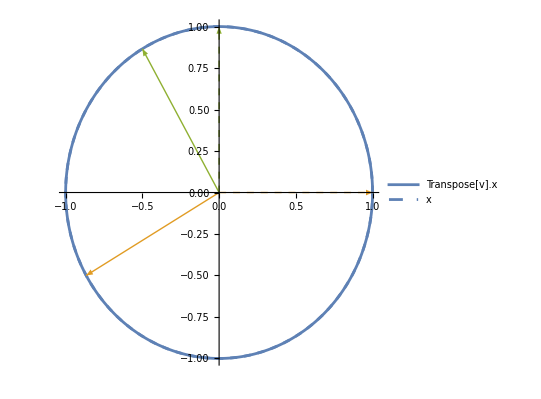

```mathematica
ParametricPlot[{Transpose[matrixV].{Cos[θ],Sin[θ]},{Cos[θ],Sin[θ]}},{θ,0,2 Pi},Sequence[PlotLegends->{HoldForm[Dot[Transpose[v],x]],HoldForm[x]},PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thick],Directive[RGBColor[0.368417,0.506779,0.709798],Thick,Dashed]},Epilog->MapThread[{Thick,#2,Arrow[{{0,0},Dot[Transpose[matrixV],#]}],Dashed,Arrow[{{0,0},#}]}&,{IdentityMatrix[2],{RGBColor[0.880722,0.611041,0.142051],RGBColor[0.560181,0.691569,0.194885]}}]]]
```

为沿轴的缩放

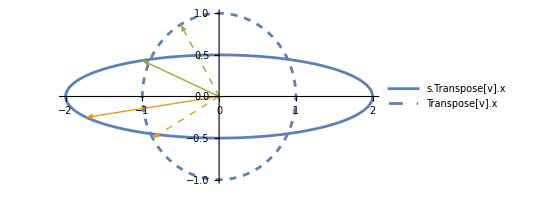

```mathematica
ParametricPlot[{matrixS.Transpose[matrixV].{Cos[θ],Sin[θ]},Transpose[matrixV].{Cos[θ],Sin[θ]}},{θ,0,2 π},Sequence[PlotLegends->{HoldForm[Dot[s,Transpose[v],x]],HoldForm[Dot[Transpose[v],x]]},PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thick],Directive[RGBColor[0.368417,0.506779,0.709798],Thick,Dashed]},Epilog->MapThread[{Thick,#2,Arrow[{{0,0},Dot[matrixS,Transpose[matrixV],#]}],Dashed,Arrow[{{0,0},Dot[Transpose[matrixV],#]}]}&,{IdentityMatrix[2],{RGBColor[0.880722,0.611041,0.142051],RGBColor[0.560181,0.691569,0.194885]}}]]]
```

为旋转（加反射）矩阵

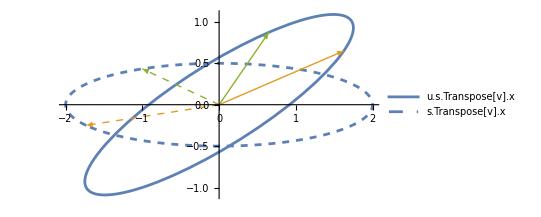

```mathematica
ParametricPlot[{matrixU.matrixS.Transpose[matrixV].{Cos[θ],Sin[θ]},matrixS.Transpose[matrixV].{Cos[θ],Sin[θ]}},{θ,0,2 π},Sequence[PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thick],Directive[RGBColor[0.368417,0.506779,0.709798],Thick,Dashed]},PlotLegends->{HoldForm[Dot[u,s,Transpose[v],x]],HoldForm[Dot[s,Transpose[v],x]]},Epilog->MapThread[{Thick,#2,Arrow[{{0,0},Dot[matrixU,matrixS,Transpose[matrixV],#]}],Dashed,Arrow[{{0,0},Dot[matrixS,Transpose[matrixV],#]}]}&,{IdentityMatrix[2],{RGBColor[0.880722,0.611041,0.142051],RGBColor[0.560181,0.691569,0.194885]}}]]]
```

格拉姆矩阵

数据矩阵向规范正交基投影
 对数据矩阵SVD分解
 可知  的格拉姆矩阵为对角阵

```mathematica
xmatrix=Transpose@{sepalLength,sepalWidth,petalLength,petalWidth};
```

```mathematica
Transpose[#].#&@SingularValueDecomposition[xmatrix][[2]] (*S^TS*)
```

{{9208.31,0.,0.,0.},{0.,315.454,0.,0.},{0.,0.,11.978,0.},{0.,0.,0.,3.55257}}

```mathematica
vmatrix=Transpose@Eigenvectors[irisGram];(*V矩阵*)
zmatrix=xmatrix.vmatrix;
lamatrix=Transpose@zmatrix.zmatrix(*之前算的Z^TZ*)
```

{{9208.31,2.31637×10^-12,1.02141×10^-14,1.47682×10^-12},{2.31637×10^-12,315.454,-9.75997×10^-13,-7.84178×10^-13},{1.02141×10^-14,-9.75997×10^-13,11.978,1.32856×10^-12},{1.47682×10^-12,-7.84178×10^-13,1.32856×10^-12,3.55257}}

```mathematica
Transpose[#].#&[xmatrix.SingularValueDecomposition[xmatrix][[3]]](*此时算的Z^TZ*)
```

{{9208.31,6.50147×10^-13,-5.2669×10^-13,-4.60298×10^-13},{6.50147×10^-13,315.454,3.86358×10^-14,-1.04472×10^-13},{-5.2669×10^-13,3.86358×10^-14,11.978,-6.47399×10^-15},{-4.60298×10^-13,-1.04472×10^-13,-6.47399×10^-15,3.55257}}

截断型SVD分解

```mathematica
dataLena=ImageData@ColorConvert[Import["ExampleData/lena.tif"],"Grayscale"];
```

```mathematica
Image[#[[1]].#[[2]].Transpose[#[[3]]]]&@SingularValueDecomposition[dataLena,#](*截断型SVD分解后重构*)&/@Range[15](*取前p个奇异值截断*)//ArrayReshape[#,{3,5}]&//GraphicsGrid(*显示行列数*)//Show[#,ImageSize->Large]&(*图像尺寸大*)
```

-Graphics-